# Fourier Analysis

## Transformada de Fourier

With the setting FourierParameters ⟶ {a, b} the Fourier transform computed by FourierTransform is √((|b|)/(2π)^(1-a))∫_(-∞)^∞ f(t)ⅇ^(ⅈ b ω t)ⅆt.

Some common choices for {a, b} are {0, 1} (default; modern physics), {1, -1} (pure mathematics; systems engineering), {-1, 1} (classical physics), and {0, -2 π} (signal processing) .

```mathematica
FourierTransform[Exp[-Abs[a t]],t,ω]
```

(√(2/π) Abs[a])/(ω^2+Abs[a]^2)

```mathematica
FourierTransform[Exp[-Abs[a t]],t,ω,FourierParameters->{0,-1}]
```

(√(2/π) Abs[a])/(ω^2+Abs[a]^2)

```mathematica
FourierTransform[Exp[-Abs[a t]],t,ω,FourierParameters->{-1,1}]
```

Abs[a]/(π (ω^2+Abs[a]^2))

## Discrete Fourier Transform

### Definitions

-Graphics-

### Fourier

```mathematica
ur=RandomReal[{0,1},10]
```

{0.951457,0.619307,0.437938,0.747434,0.0284468,0.581348,0.635549,0.269337,0.242052,0.233316}

```mathematica
vs1=Fourier[ur]
```

{1.50088+0. ⅈ,0.132386+0.161602 ⅈ,0.19883+0.246217 ⅈ,0.184766-0.191775 ⅈ,0.262521+0.269465 ⅈ,-0.0491098+0. ⅈ,0.262521-0.269465 ⅈ,0.184766+0.191775 ⅈ,0.19883-0.246217 ⅈ,0.132386-0.161602 ⅈ}

```mathematica
InverseFourier[vs1]
```

{0.951457,0.619307,0.437938,0.747434,0.0284468,0.581348,0.635549,0.269337,0.242052,0.233316}

```mathematica
vs2=Fourier[ur,FourierParameters->{-1,1}]
```

{0.474619+0. ⅈ,0.041864+0.051103 ⅈ,0.0628757+0.0778607 ⅈ,0.0584281-0.0606447 ⅈ,0.0830163+0.0852124 ⅈ,-0.0155299+0. ⅈ,0.0830163-0.0852124 ⅈ,0.0584281+0.0606447 ⅈ,0.0628757-0.0778607 ⅈ,0.041864-0.051103 ⅈ}

```mathematica
InverseFourier[vs2,FourierParameters->{-1,1}]
```

{0.951457,0.619307,0.437938,0.747434,0.0284468,0.581348,0.635549,0.269337,0.242052,0.233316}

### Fourier Matrix

```mathematica
With[{n=3},Table[1/n^(1/2)ⅇ^((2π i(r-1)(s-1))/n),{r,1,n},{s,1,n}]]//MatrixForm
```

(1/(√3) | 1/(√3) | 1/(√3)
1/(√3) | ⅇ^((2 i π)/3)/(√3) | ⅇ^((4 i π)/3)/(√3)
1/(√3) | ⅇ^((4 i π)/3)/(√3) | ⅇ^((8 i π)/3)/(√3))

```mathematica
FourierMatrix[3]//MatrixForm
```

(1/(√3) | 1/(√3) | 1/(√3)
1/(√3) | ⅇ^((2 ⅈ π)/3)/(√3) | ⅇ^(-(2 ⅈ π)/3)/(√3)
1/(√3) | ⅇ^(-(2 ⅈ π)/3)/(√3) | ⅇ^((2 ⅈ π)/3)/(√3))

```mathematica
FourierMatrix[3].{1,2,3}
```

{2 √3,1/(√3)+√3 ⅇ^(-(2 ⅈ π)/3)+(2 ⅇ^((2 ⅈ π)/3))/(√3),1/(√3)+(2 ⅇ^(-(2 ⅈ π)/3))/(√3)+√3 ⅇ^((2 ⅈ π)/3)}

```mathematica
FourierMatrix[3,WorkingPrecision->MachinePrecision].{1,2,3}
```

{3.4641+0. ⅈ,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ}

```mathematica
Fourier[{1,2,3}]
```

{3.4641+0. ⅈ,-0.866025-0.5 ⅈ,-0.866025+0.5 ⅈ}

## Fourier Series Convergence

```mathematica
Manipulate[Plot[stepFSeries[x,nmax],{x,-π,π},PlotRange->{-2,2}],{nmax,1,30,5}]
```

```mathematica
Manipulate[Plot[absFSeries[x,nmax],{x,-π,π},PlotRange->{-0.5,4}],{nmax,1,20,1}]
```

## DFT

```mathematica
triangle[t_,a_]:=Piecewise[{{a*(1-a Abs[t]), Abs[t]<1/a}, {0, Abs[t]>1/a}}]
```

```mathematica
FTtriangle[ω_,a_]=FourierTransform[triangle[t,a],t,ω]//FullSimplify
```

(a^2 √(2/π) (-1+Cos[ω/a]) (-1+UnitStep[-a]))/ω^2

```mathematica
Manipulate[GraphicsGrid[{{
Plot[triangle[t,a],{t,-6,6},PlotRange->{{-6,6},{0,2}}],
Plot[FTtriangle[t,a],{t,-20,20},PlotRange->{{-25,25},{0,1}}]}}],
{a,0.1,2,0.1}]
```

```mathematica
triangleSampling=Table[{x,triangle[x,1]},{x,-2.,2.,0.01}];
```

```mathematica
Ν=Length[triangleSampling]
```

401

```mathematica
fourierList=1/Ν Fourier[triangleSampling[[All,2]]];
```

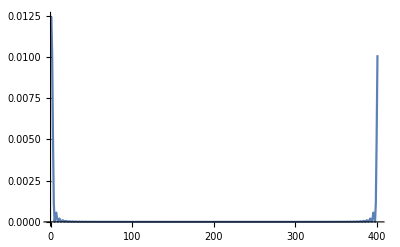

```mathematica
ListLinePlot[Abs[fourierList],PlotRange->All]
```

```mathematica
c0=First[fourierList]//Chop;
cn=Rest[fourierList];
cnconj=Conjugate[cn];
an=Take[cn+cnconj//Chop,Floor[Ν/2]];
bn=Take[(cn-cnconj)ⅈ//Chop,Floor[Ν/2]];
fourierSum[x_]:=c0+an.Table[Cos[k x],{k,1,Floor[Ν/2]}]+bn.Table[Sin[k x],{k,1,Floor[Ν/2]}];
```

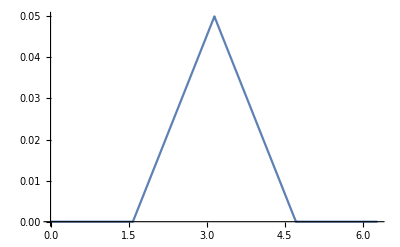

```mathematica
Plot[Evaluate[fourierSum[x]],{x,0,2π},PlotRange->Automatic]
```

## Power Spectrum

```mathematica
Clear[f];
```

```mathematica
ω=2π;
f[t_]:=Sin[ω t]+Sin[5 ω t]
```

{0.628319,40.2124}

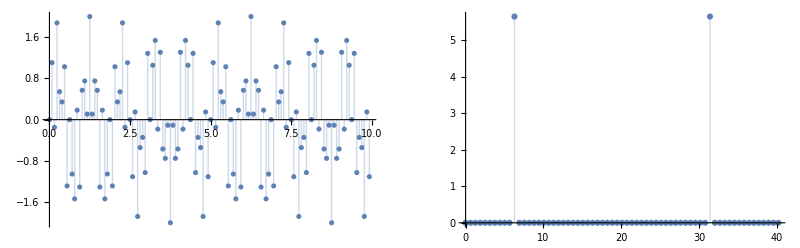

```mathematica
plotPowerSpectrum[f[t],t,128,10]
```

### Aliasing

{0.628319,20.1062}

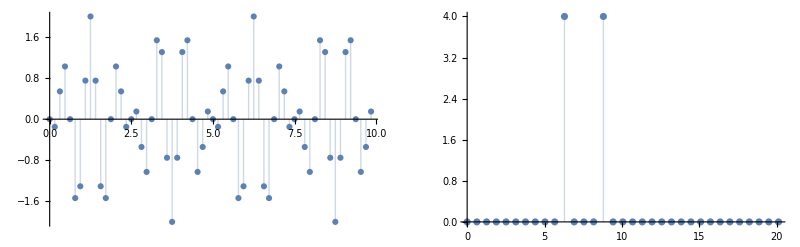

```mathematica
plotPowerSpectrum[f[t],t,64,10]
```

### Leakage

{0.610018,39.0412}

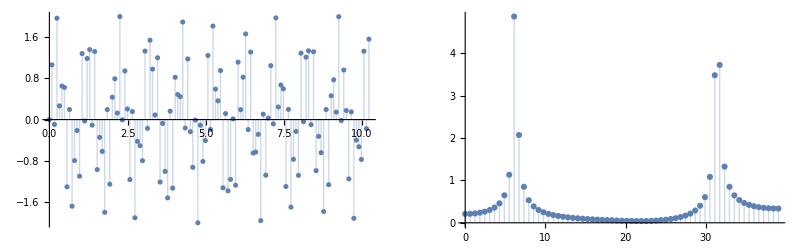

```mathematica
plotPowerSpectrum[f[t],t,128,10.3]
```

```mathematica
(*dtt=10/128;
tt=N@Table[t,{t,0,10-dtt,dtt}];
ff=N@Table[f[t],{t,0,10-dtt,dtt}];
Show[ListPlot[Transpose[{tt,ff}]],Plot[f[t],{t,0,10}]]*)
```